```mathematica
file1 = "G:\\Studia\\IV\\MO\\Laboratoria\\9\\Program91\\Program9\\results_three0.dat";
file2 = "G:\\Studia\\IV\\MO\\Laboratoria\\9\\Program91\\Program9\\results_three1.dat";
file3 = "G:\\Studia\\IV\\MO\\Laboratoria\\9\\Program91\\Program9\\results_three2.dat";
file4= "G:\\Studia\\IV\\MO\\Laboratoria\\9\\Program91\\Program9\\results_numerow0.dat";
file5 = "G:\\Studia\\IV\\MO\\Laboratoria\\9\\Program91\\Program9\\results_numerow1.dat";
file6 = "G:\\Studia\\IV\\MO\\Laboratoria\\9\\Program91\\Program9\\results_numerow2.dat";
errorthreepoints = "G:\\Studia\\IV\\MO\\Laboratoria\\9\\Program91\\Program9\\errors_three.dat";
errornumerow = "G:\\Studia\\IV\\MO\\Laboratoria\\9\\Program91\\Program9\\errors_numerow.dat";
```

```mathematica
res1 = ReadList[file1, {Real, Real}];
res2 = ReadList[file2, {Real, Real}];
res3 = ReadList[file3, {Real, Real}];
res4 = ReadList[file4, {Real, Real}];
res5= ReadList[file5, {Real, Real}];
res6 = ReadList[file6, {Real, Real}];
errorsthreepoints= ReadList[errorthreepoints, {Real, Real}]
errorsnumerow= ReadList[errornumerow, {Real, Real}]
```

{{-0.40594,-1.765},{-1.82091,-4.60392},{-2.11351,-5.18912},{-2.28675,-5.5356},{-2.41026,-5.78261},{-2.50631,-5.97471},{-2.58492,-6.13192},{-2.65145,-6.265},{-2.70914,-6.38036},{-2.76005,-6.48219},{-2.80561,-6.57332},{-2.84685,-6.65579},{-2.88451,-6.7311},{-2.91916,-6.80041},{-2.95125,-6.86458},{-2.98113,-6.92435},{-3.00908,-6.98026},{-3.03535,-7.03279},{-3.06012,-7.08232},{-3.08355,-7.12918},{-3.10578,-7.17365},{-3.12693,-7.21594},{-3.14709,-7.25627},{-3.16636,-7.29481},{-3.18481,-7.33172},{-3.20251,-7.36712},{-3.21952,-7.40114},{-3.23589,-7.43387},{-3.25166,-7.4654},{-3.26688,-7.49583},{-3.28158,-7.52526},{-3.2958,-7.55369},{-3.30957,-7.58123},{-3.32292,-7.60798},{-3.33587,-7.63384},{-3.34844,-7.65896},{-3.36066,-7.68341},{-3.37255,-7.7072},{-3.38412,-7.73036},{-3.39539,-7.7529},{-3.40637,-7.77485},{-3.41709,-7.79626},{-3.42754,-7.81713},{-3.43775,-7.83754},{-3.44773,-7.85756},{-3.45748,-7.8771},{-3.46702,-7.89613},{-3.47635,-7.91484},{-3.48548,-7.93293},{-3.49443,-7.95096},{-3.5032,-7.96847},{-3.51179,-7.98563},{-3.52022,-8.00249},{-3.52848,-8.01907},{-3.5366,-8.03528},{-3.54456,-8.05132},{-3.55238,-8.06665},{-3.56006,-8.08226},{-3.56761,-8.0974},{-3.57503,-8.11206},{-3.58232,-8.12687},{-3.58949,-8.14108},{-3.59655,-8.15527},{-3.6035,-8.16933},{-3.61033,-8.18276},{-3.61706,-8.19619},{-3.62369,-8.20972},{-3.63021,-8.22279},{-3.63664,-8.23562},{-3.64298,-8.24823},{-3.64923,-8.26031},{-3.65538,-8.27339},{-3.66145,-8.28509},{-3.66744,-8.29657},{-3.67335,-8.3086},{-3.67917,-8.32069},{-3.68492,-8.33153},{-3.6906,-8.34288},{-3.6962,-8.35487},{-3.70173,-8.36572},{-3.70719,-8.37641},{-3.71258,-8.38774},{-3.71791,-8.39798},{-3.72317,-8.40786},{-3.72837,-8.41915},{-3.7335,-8.42921},{-3.73858,-8.43889},{-3.7436,-8.44903},{-3.74856,-8.459},{-3.75347,-8.46828},{-3.75832,-8.47926},{-3.76311,-8.48835},{-3.76786,-8.498},{-3.77255,-8.50737},{-3.77719,-8.51615},{-3.78179,-8.52571},{-3.78633,-8.53465},{-3.79083,-8.54286},{-3.79528,-8.55264},{-3.79969,-8.56053},{-3.80405,-8.56985},{-3.80837,-8.57819},{-3.81265,-8.58606},{-3.81689,-8.59574},{-3.82108,-8.6038},{-3.82523,-8.61501},{-3.82935,-8.62153},{-3.83343,-8.62802},{-3.83746,-8.63748},{-3.84147,-8.64323},{-3.84543,-8.65231},{-3.84936,-8.66017},{-3.85325,-8.66827},{-3.85711,-8.67529},{-3.86094,-8.68363},{-3.86473,-8.69054},{-3.86849,-8.70163},{-3.87221,-8.70534},{-3.87591,-8.71241},{-3.87957,-8.72054},{-3.88321,-8.72965},{-3.88681,-8.73452},{-3.89038,-8.74244},{-3.89393,-8.74861},{-3.89744,-8.75652},{-3.90093,-8.7619},{-3.90439,-8.77025},{-3.90782,-8.77818},{-3.91123,-8.78251},{-3.9146,-8.78957},{-3.91796,-8.80241},{-3.92128,-8.80516},{-3.92459,-8.81797},{-3.92786,-8.81555},{-3.93111,-8.82386},{-3.93434,-8.82881},{-3.93755,-8.84027},{-3.94073,-8.84594},{-3.94389,-8.8515},{-3.94702,-8.84947},{-3.95013,-8.86764},{-3.95322,-8.86687},{-3.95629,-8.8746},{-3.95934,-8.87795},{-3.96236,-8.88326},{-3.96537,-8.89462},{-3.96835,-8.89763},{-3.97132,-8.90112},{-3.97426,-8.92026},{-3.97718,-8.91876},{-3.98009,-8.9205},{-3.98297,-8.9299},{-3.98584,-8.92988},{-3.98869,-8.93901},{-3.99151,-8.93861},{-3.99432,-8.9428},{-3.99712,-8.95474},{-3.99989,-8.9627},{-4.00265,-8.96761},{-4.00539,-8.98341},{-4.00811,-8.9742},{-4.01081,-8.98045},{-4.0135,-8.99098},{-4.01617,-8.98663},{-4.01883,-8.99821},{-4.02147,-9.00462},{-4.02409,-9.00921},{-4.0267,-9.01643},{-4.02929,-9.02188},{-4.03187,-9.02307},{-4.03443,-9.0322},{-4.03698,-9.02496},{-4.03951,-9.04507},{-4.04203,-9.04155},{-4.04453,-9.0504},{-4.04702,-9.05588},{-4.04949,-9.06078},{-4.05195,-9.06934},{-4.0544,-9.06666},{-4.05683,-9.07401},{-4.05925,-9.08511},{-4.06165,-9.08955},{-4.06405,-9.0775},{-4.06643,-9.09388},{-4.06879,-9.08289},{-4.07115,-9.11779},{-4.07349,-9.12143},{-4.07581,-9.1124},{-4.07813,-9.12475},{-4.08043,-9.11646},{-4.08273,-9.13121},{-4.085,-9.12871},{-4.08727,-9.11941},{-4.08953,-9.12717},{-4.09177,-9.14904},{-4.094,-9.14977},{-4.09622,-9.1504},{-4.09843,-9.16491},{-4.10063,-9.1815},{-4.10282,-9.15102},{-4.105,-9.17918},{-4.10716,-9.18866},{-4.10932,-9.18585},{-4.11146,-9.17664},{-4.1136,-9.20009},{-4.11572,-9.18511},{-4.11783,-9.18356},{-4.11993,-9.18032},{-4.12203,-9.21552},{-4.12411,-9.20798},{-4.12618,-9.2215},{-4.12824,-9.20008},{-4.1303,-9.23069},{-4.13234,-9.24007},{-4.13438,-9.2341},{-4.1364,-9.26796},{-4.13841,-9.21847},{-4.14042,-9.25987},{-4.14242,-9.27221},{-4.1444,-9.25027},{-4.14638,-9.27073},{-4.14835,-9.26076},{-4.15031,-9.25535},{-4.15226,-9.27399},{-4.15421,-9.29492},{-4.15614,-9.275},{-4.15807,-9.28659},{-4.15998,-9.29013},{-4.16189,-9.28535},{-4.16379,-9.29854},{-4.16568,-9.3016},{-4.16757,-9.29793},{-4.16944,-9.29498},{-4.17131,-9.28285},{-4.17317,-9.27627},{-4.17502,-9.32063},{-4.17687,-9.3247},{-4.1787,-9.31709},{-4.18053,-9.34504},{-4.18235,-9.33018},{-4.18416,-9.31242},{-4.18597,-9.32505},{-4.18777,-9.38541},{-4.18956,-9.32715},{-4.19134,-9.32509},{-4.19312,-9.35357},{-4.19489,-9.3493},{-4.19665,-9.34217},{-4.1984,-9.35954},{-4.20015,-9.351},{-4.20189,-9.37778},{-4.20362,-9.36247},{-4.20535,-9.3846},{-4.20707,-9.38938},{-4.20878,-9.39488},{-4.21049,-9.3781},{-4.21219,-9.37052},{-4.21388,-9.39351},{-4.21557,-9.38727},{-4.21725,-9.40686},{-4.21892,-9.41491},{-4.22059,-9.40635},{-4.22225,-9.42225},{-4.2239,-9.43998},{-4.22555,-9.44102},{-4.22719,-9.40901},{-4.22883,-9.43541},{-4.23046,-9.47264},{-4.23208,-9.43823},{-4.2337,-9.41812},{-4.23531,-9.4244},{-4.23691,-9.40036},{-4.23851,-9.46857},{-4.24011,-9.43138},{-4.24169,-9.44682},{-4.24328,-9.49197},{-4.24485,-9.46661},{-4.24642,-9.47078},{-4.24799,-9.50547},{-4.24955,-9.42983},{-4.2511,-9.47596},{-4.25265,-9.53179},{-4.25419,-9.46214},{-4.25573,-9.42368},{-4.25726,-9.44732},{-4.25879,-9.48539},{-4.26031,-9.5058},{-4.26182,-9.59282},{-4.26333,-9.47702},{-4.26484,-9.49483},{-4.26634,-9.44424},{-4.26783,-9.46589},{-4.26932,-9.50331},{-4.27081,-9.49791},{-4.27229,-9.50736},{-4.27376,-9.52627},{-4.27523,-9.49561},{-4.2767,-9.59093},{-4.27815,-9.55015},{-4.27961,-9.498},{-4.28106,-9.46802},{-4.2825,-9.49711},{-4.28394,-9.50183},{-4.28538,-9.58955},{-4.28681,-9.5195},{-4.28824,-9.57601},{-4.28966,-9.52132},{-4.29108,-9.53372},{-4.29249,-9.6108},{-4.29389,-9.52042},{-4.2953,-9.4976},{-4.2967,-9.53848},{-4.29809,-9.56603},{-4.29948,-9.56797},{-4.30087,-9.56401},{-4.30225,-9.53705},{-4.30362,-9.59943},{-4.30499,-9.65939},{-4.30636,-9.57679},{-4.30773,-9.63341},{-4.30908,-9.68183},{-4.31044,-9.65534},{-4.31179,-9.63955},{-4.31314,-9.5663},{-4.31448,-9.66261},{-4.31582,-9.57966},{-4.31715,-9.6463},{-4.31848,-9.63755},{-4.31981,-9.64072},{-4.32113,-9.66613},{-4.32245,-9.73394},{-4.32376,-9.61587},{-4.32507,-9.66027},{-4.32638,-9.66575},{-4.32768,-9.50548},{-4.32898,-9.62901},{-4.33027,-9.68757},{-4.33156,-9.59113},{-4.33285,-9.54505},{-4.33413,-9.48319},{-4.33541,-9.56124},{-4.33669,-9.726},{-4.33796,-9.70275},{-4.33922,-9.63245},{-4.34049,-9.59005},{-4.34175,-9.62004},{-4.34301,-9.68152},{-4.34426,-9.66743},{-4.34551,-9.56279},{-4.34676,-9.73574},{-4.348,-9.6679},{-4.34924,-9.6165},{-4.35047,-9.57346},{-4.3517,-9.73385},{-4.35293,-9.79123},{-4.35416,-9.6457},{-4.35538,-9.72247},{-4.3566,-9.59687},{-4.35781,-9.63648},{-4.35902,-9.65036},{-4.36023,-9.72702},{-4.36144,-9.72526},{-4.36264,-9.818},{-4.36383,-9.78023},{-4.36503,-9.90823},{-4.36622,-9.6925},{-4.36741,-9.80745},{-4.36859,-9.74398},{-4.36978,-9.7537},{-4.37095,-9.83531},{-4.37213,-9.69192},{-4.3733,-9.75208},{-4.37447,-9.57054},{-4.37564,-9.97058},{-4.3768,-9.8645},{-4.37796,-9.8287},{-4.37911,-9.75366},{-4.38027,-9.8459},{-4.38142,-9.61618},{-4.38257,-9.82547},{-4.38371,-10.0458},{-4.38485,-9.85958},{-4.38599,-9.68043},{-4.38712,-9.71117},{-4.38826,-9.90809},{-4.38939,-9.93309},{-4.39051,-9.92115},{-4.39164,-9.82812},{-4.39276,-9.77966},{-4.39387,-9.94255},{-4.39499,-10.4524},{-4.3961,-9.60307},{-4.39721,-9.67661},{-4.39832,-9.773},{-4.39942,-9.61698},{-4.40052,-9.8304},{-4.40162,-9.69284},{-4.40271,-9.95137},{-4.40381,-9.95641},{-4.4049,-9.83071},{-4.40598,-9.69079},{-4.40707,-9.83271},{-4.40815,-9.65144},{-4.40923,-9.73993},{-4.4103,-9.87731},{-4.41138,-9.8359},{-4.41245,-9.91153},{-4.41352,-9.81732},{-4.41458,-9.90139},{-4.41565,-9.86963},{-4.41671,-9.78143},{-4.41776,-9.75643},{-4.41882,-10.041},{-4.41987,-9.62609},{-4.42092,-10.0296},{-4.42197,-9.73359},{-4.42302,-9.91959},{-4.42406,-9.80031},{-4.4251,-9.86925},{-4.42614,-10.2113},{-4.42717,-9.90019},{-4.4282,-9.85694},{-4.42923,-10.2367},{-4.43026,-10.2853},{-4.43129,-9.62966},{-4.43231,-9.83266},{-4.43333,-9.9516},{-4.43435,-10.06},{-4.43536,-9.68266},{-4.43638,-9.86484},{-4.43739,-9.74206},{-4.4384,-9.80603},{-4.4394,-9.97081},{-4.44041,-9.71045},{-4.44141,-9.87152},{-4.44241,-9.94426},{-4.44341,-9.98347},{-4.4444,-10.4278},{-4.44539,-10.4495},{-4.44638,-9.88899},{-4.44737,-10.0886},{-4.44836,-9.92057},{-4.44934,-9.871},{-4.45032,-10.8772},{-4.4513,-10.0619},{-4.45228,-10.0013},{-4.45325,-10.148},{-4.45423,-10.4496},{-4.4552,-9.96611},{-4.45617,-9.91147},{-4.45713,-10.0772},{-4.4581,-10.0991},{-4.45906,-9.98634},{-4.46002,-10.0148},{-4.46097,-10.1223},{-4.46193,-9.65106},{-4.46288,-9.6975},{-4.46383,-9.94035},{-4.46478,-10.1087},{-4.46573,-9.98852},{-4.46668,-9.71164},{-4.46762,-9.99923},{-4.46856,-9.95568},{-4.4695,-10.0209},{-4.47044,-9.76327},{-4.47137,-9.91189},{-4.4723,-10.7292},{-4.47323,-10.1698},{-4.47416,-11.0184},{-4.47509,-9.72342},{-4.47601,-9.87914},{-4.47694,-9.7579},{-4.47786,-9.69149},{-4.47878,-10.1957},{-4.4797,-10.0554},{-4.48061,-10.067},{-4.48152,-10.1277},{-4.48243,-9.94502},{-4.48334,-9.91113},{-4.48425,-10.5473},{-4.48516,-10.1567},{-4.48606,-9.85578},{-4.48696,-10.029},{-4.48786,-10.1636},{-4.48876,-9.83707},{-4.48966,-10.9226},{-4.49055,-10.1922},{-4.49144,-9.74392},{-4.49234,-9.86165},{-4.49322,-9.74066},{-4.49411,-10.0295},{-4.495,-9.79058},{-4.49588,-10.3926},{-4.49676,-10.1045},{-4.49764,-10.0518},{-4.49852,-10.1415},{-4.4994,-10.0781},{-4.50027,-9.88591},{-4.50114,-9.85869},{-4.50202,-9.93066},{-4.50288,-10.2996},{-4.50375,-9.93209},{-4.50462,-9.76933},{-4.50548,-10.253},{-4.50635,-10.4082},{-4.50721,-9.96588},{-4.50806,-9.93588},{-4.50892,-9.87379},{-4.50978,-10.2705},{-4.51063,-10.054},{-4.51148,-9.87588},{-4.51234,-10.328},{-4.51318,-9.73717},{-4.51403,-10.1144},{-4.51488,-10.4822},{-4.51572,-10.0931},{-4.51656,-10.112},{-4.5174,-10.484},{-4.51824,-10.4606},{-4.51908,-9.89926},{-4.51992,-10.1692},{-4.52075,-10.3566},{-4.52158,-10.0807},{-4.52242,-10.2919},{-4.52324,-9.765},{-4.52407,-9.92672},{-4.5249,-9.84457},{-4.52572,-9.83029},{-4.52655,-10.2713},{-4.52737,-10.237},{-4.52819,-10.7182},{-4.52901,-9.74908},{-4.52982,-9.67529},{-4.53064,-9.9063},{-4.53145,-10.2346},{-4.53227,-10.0434},{-4.53308,-9.71193},{-4.53389,-9.93788},{-4.53469,-9.79592},{-4.5355,-9.66213},{-4.53631,-10.8696},{-4.53711,-10.0972},{-4.53791,-9.63745},{-4.53871,-10.2999},{-4.53951,-9.88351},{-4.54031,-10.1403},{-4.5411,-10.1589},{-4.5419,-10.2646},{-4.54269,-9.93531},{-4.54348,-9.7877},{-4.54427,-9.77915},{-4.54506,-10.0292},{-4.54585,-9.84488},{-4.54664,-9.87762},{-4.54742,-9.52439},{-4.5482,-9.66702},{-4.54899,-10.3264},{-4.54977,-9.92822},{-4.55055,-10.4412},{-4.55132,-10.2116},{-4.5521,-10.6497},{-4.55287,-9.8353},{-4.55365,-10.0116},{-4.55442,-10.572},{-4.55519,-10.1329},{-4.55596,-10.1481},{-4.55673,-9.73415},{-4.55749,-10.6274},{-4.55826,-9.84202},{-4.55902,-9.9052},{-4.55979,-10.4108},{-4.56055,-9.82058},{-4.56131,-10.3373},{-4.56207,-10.4336},{-4.56282,-10.1554},{-4.56358,-10.2694},{-4.56433,-10.0816},{-4.56509,-10.1637},{-4.56584,-9.77967},{-4.56659,-9.71272},{-4.56734,-10.495},{-4.56809,-10.1026},{-4.56883,-10.098},{-4.56958,-9.97892},{-4.57032,-10.6448},{-4.57107,-10.0291},{-4.57181,-10.2939},{-4.57255,-10.3421},{-4.57329,-10.2454},{-4.57402,-10.0301},{-4.57476,-10.1739},{-4.5755,-9.92901},{-4.57623,-10.0019},{-4.57696,-10.3249},{-4.5777,-9.71259},{-4.57843,-9.45266},{-4.57916,-10.541},{-4.57988,-10.3738},{-4.58061,-10.2169},{-4.58134,-10.2975},{-4.58206,-10.0553},{-4.58278,-9.87097},{-4.58351,-10.3849},{-4.58423,-10.093},{-4.58495,-9.83763},{-4.58566,-10.1593},{-4.58638,-10.3673},{-4.5871,-9.8802},{-4.58781,-9.82321},{-4.58853,-10.5072},{-4.58924,-9.782},{-4.58995,-10.0245},{-4.59066,-10.5909},{-4.59137,-10.386},{-4.59208,-10.8358},{-4.59278,-10.1981},{-4.59349,-9.99177},{-4.59419,-10.0092},{-4.5949,-10.6454},{-4.5956,-9.97939},{-4.5963,-10.9095},{-4.597,-10.1175},{-4.5977,-9.58118},{-4.5984,-9.74627},{-4.59909,-10.1226},{-4.59979,-10.142},{-4.60048,-9.99344},{-4.60118,-9.86958},{-4.60187,-10.0408},{-4.60256,-10.1251},{-4.60325,-10.0682},{-4.60394,-10.5671},{-4.60462,-10.4567},{-4.60531,-10.1972},{-4.606,-10.357},{-4.60668,-10.3559},{-4.60736,-9.74984},{-4.60805,-9.83352},{-4.60873,-9.96601},{-4.60941,-10.0896},{-4.61009,-10.0907},{-4.61077,-10.3749},{-4.61144,-10.0161},{-4.61212,-9.95116},{-4.61279,-10.6851},{-4.61347,-10.2443},{-4.61414,-10.15},{-4.61481,-10.6216},{-4.61548,-10.7766},{-4.61615,-10.1039},{-4.61682,-9.94205},{-4.61749,-10.6406},{-4.61815,-10.7491},{-4.61882,-10.0828},{-4.61948,-10.7365},{-4.62015,-9.94943},{-4.62081,-10.1208},{-4.62147,-9.85217},{-4.62213,-9.73173},{-4.62279,-10.1584},{-4.62345,-10.1294},{-4.62411,-9.69429},{-4.62476,-10.207},{-4.62542,-10.3812},{-4.62607,-10.6123},{-4.62673,-10.4165},{-4.62738,-10.1118},{-4.62803,-10.3864},{-4.62868,-10.2865},{-4.62933,-10.4519},{-4.62998,-10.3524},{-4.63063,-9.93824},{-4.63128,-10.5032},{-4.63192,-10.0634},{-4.63257,-10.2166},{-4.63321,-10.3283},{-4.63385,-9.73238},{-4.63449,-10.2657},{-4.63514,-11.0507},{-4.63578,-9.862},{-4.63641,-9.83918},{-4.63705,-9.98124},{-4.63769,-10.7231},{-4.63833,-9.88358},{-4.63896,-9.71725},{-4.6396,-10.2917},{-4.64023,-10.2835},{-4.64086,-9.84967},{-4.64149,-10.4426},{-4.64212,-10.078},{-4.64275,-10.0348},{-4.64338,-10.3368},{-4.64401,-10.1503},{-4.64464,-10.0629},{-4.64526,-9.89891},{-4.64589,-10.5811},{-4.64651,-10.0993},{-4.64714,-10.1274},{-4.64776,-9.74256},{-4.64838,-9.97246},{-4.649,-9.9367},{-4.64962,-9.99013},{-4.65024,-10.1837},{-4.65086,-9.58821},{-4.65148,-10.3963},{-4.65209,-10.5141},{-4.65271,-9.78434},{-4.65332,-10.5601},{-4.65394,-10.8626},{-4.65455,-10.0109},{-4.65516,-10.0104},{-4.65577,-9.86293},{-4.65638,-10.6278},{-4.65699,-10.0701},{-4.6576,-10.033},{-4.65821,-10.0432},{-4.65882,-9.6307},{-4.65942,-10.0486},{-4.66003,-10.1244},{-4.66063,-9.79932},{-4.66124,-9.91584},{-4.66184,-10.2888},{-4.66244,-10.2142},{-4.66304,-9.79433},{-4.66364,-9.76554},{-4.66424,-10.3023},{-4.66484,-10.6611},{-4.66544,-9.65396},{-4.66604,-10.3301},{-4.66663,-9.83618},{-4.66723,-10.379},{-4.66782,-9.86829},{-4.66841,-10.0053},{-4.66901,-9.83686},{-4.6696,-10.1921},{-4.67019,-10.6327},{-4.67078,-9.86442},{-4.67137,-9.70196},{-4.67196,-9.72675},{-4.67255,-9.66674},{-4.67314,-10.5359},{-4.67372,-9.77218},{-4.67431,-10.1469},{-4.67489,-9.61151},{-4.67548,-9.67751},{-4.67606,-10.1213},{-4.67664,-9.76736},{-4.67722,-10.3968},{-4.6778,-9.62275},{-4.67839,-10.2853},{-4.67896,-10.1625},{-4.67954,-10.359},{-4.68012,-9.94556},{-4.6807,-9.6253},{-4.68127,-9.66876},{-4.68185,-10.1435},{-4.68242,-10.0919},{-4.683,-10.4456},{-4.68357,-10.322},{-4.68414,-9.89291},{-4.68472,-9.89052},{-4.68529,-9.96453},{-4.68586,-9.68343},{-4.68643,-9.74771},{-4.687,-9.66054},{-4.68756,-10.0682},{-4.68813,-9.81194},{-4.6887,-10.4489},{-4.68926,-9.50815},{-4.68983,-9.73289},{-4.69039,-9.70044},{-4.69096,-9.72668},{-4.69152,-10.0877},{-4.69208,-10.3404},{-4.69264,-9.86087},{-4.6932,-9.94792},{-4.69376,-10.5238},{-4.69432,-10.2664},{-4.69488,-10.4491},{-4.69544,-9.59764},{-4.696,-10.1673},{-4.69655,-10.2627},{-4.69711,-10.2107},{-4.69766,-9.79594},{-4.69822,-10.4333},{-4.69877,-9.859},{-4.69932,-10.0752},{-4.69988,-9.91945},{-4.70043,-9.5582},{-4.70098,-9.92258},{-4.70153,-10.3267},{-4.70208,-9.77084},{-4.70263,-10.2783},{-4.70318,-10.2026},{-4.70372,-10.2867},{-4.70427,-9.69635},{-4.70482,-9.65546},{-4.70536,-10.398},{-4.7059,-9.58166},{-4.70645,-10.3568},{-4.70699,-9.79794},{-4.70753,-10.0618},{-4.70808,-9.78186},{-4.70862,-10.4056},{-4.70916,-9.75521},{-4.7097,-10.0512},{-4.71024,-9.80513},{-4.71078,-10.4579},{-4.71131,-10.2213},{-4.71185,-10.1168},{-4.71239,-9.98867},{-4.71292,-10.1627},{-4.71346,-9.5124},{-4.71399,-10.4041},{-4.71453,-10.2389},{-4.71506,-9.85227},{-4.71559,-9.71475},{-4.71612,-9.61556},{-4.71665,-9.93055},{-4.71719,-9.98678},{-4.71772,-10.0632},{-4.71824,-9.98787},{-4.71877,-10.1481},{-4.7193,-9.95878},{-4.71983,-9.47079},{-4.72036,-10.5336},{-4.72088,-10.5934},{-4.72141,-10.1436},{-4.72193,-9.65241},{-4.72246,-9.80692},{-4.72298,-9.58715},{-4.7235,-9.82777},{-4.72402,-9.93257},{-4.72455,-9.75974},{-4.72507,-10.0075},{-4.72559,-9.50746},{-4.72611,-10.0429},{-4.72663,-9.86434},{-4.72714,-10.1454},{-4.72766,-9.57883},{-4.72818,-9.84135},{-4.7287,-9.87151},{-4.72921,-9.78416},{-4.72973,-10.1528},{-4.73024,-9.70054},{-4.73076,-9.79924},{-4.73127,-9.98956},{-4.73178,-9.73582},{-4.7323,-9.97284},{-4.73281,-10.7236},{-4.73332,-9.82156},{-4.73383,-9.92262},{-4.73434,-10.4408},{-4.73485,-10.029},{-4.73536,-9.99688},{-4.73587,-9.93895},{-4.73637,-9.76388},{-4.73688,-9.98225},{-4.73739,-9.82182},{-4.73789,-9.72181},{-4.7384,-10.0253},{-4.7389,-9.4123},{-4.73941,-10.5612},{-4.73991,-10.3742},{-4.74041,-9.7919},{-4.74092,-9.959},{-4.74142,-10.0326},{-4.74192,-9.96751},{-4.74242,-10.2371},{-4.74292,-9.53977},{-4.74342,-10.8649},{-4.74392,-9.72763},{-4.74442,-9.64687},{-4.74491,-10.3119},{-4.74541,-10.2466},{-4.74591,-9.62425},{-4.7464,-10.0357},{-4.7469,-10.0705},{-4.74739,-10.3765},{-4.74789,-9.76776},{-4.74838,-11.0081},{-4.74888,-10.0787},{-4.74937,-9.73014},{-4.74986,-9.85633},{-4.75035,-9.60903},{-4.75084,-10.0056},{-4.75133,-9.78935},{-4.75182,-10.2391},{-4.75231,-9.97176},{-4.7528,-10.3362},{-4.75329,-9.7484},{-4.75378,-9.95544},{-4.75426,-10.1387},{-4.75475,-10.3727},{-4.75524,-9.85084},{-4.75572,-9.77738},{-4.75621,-9.61332},{-4.75669,-10.2033},{-4.75718,-9.79378},{-4.75766,-9.93483},{-4.75814,-10.2783},{-4.75862,-10.2575},{-4.75911,-9.86573},{-4.75959,-10.5682},{-4.76007,-10.0067},{-4.76055,-10.1225},{-4.76103,-10.2299},{-4.76151,-10.6401},{-4.76199,-10.6667},{-4.76246,-9.78715},{-4.76294,-9.83819},{-4.76342,-9.74731},{-4.76389,-10.022},{-4.76437,-9.92812},{-4.76485,-9.69818},{-4.76532,-9.81763},{-4.76579,-9.79824},{-4.76627,-9.71882},{-4.76674,-9.89919},{-4.76721,-9.88809},{-4.76769,-9.83672},{-4.76816,-10.0755},{-4.76863,-9.89218},{-4.7691,-9.60815},{-4.76957,-9.84129},{-4.77004,-9.45517},{-4.77051,-10.1509},{-4.77098,-10.9042},{-4.77145,-10.4377},{-4.77191,-10.39},{-4.77238,-9.67575},{-4.77285,-9.788},{-4.77331,-10.7024},{-4.77378,-9.86762},{-4.77425,-9.82905},{-4.77471,-9.70655},{-4.77517,-9.57696},{-4.77564,-9.80204},{-4.7761,-9.55198},{-4.77656,-9.4906},{-4.77703,-10.7238},{-4.77749,-9.85838},{-4.77795,-10.5182},{-4.77841,-9.91538},{-4.77887,-9.8215},{-4.77933,-9.95062},{-4.77979,-9.78634},{-4.78025,-9.66248},{-4.78071,-10.1995},{-4.78116,-9.88096},{-4.78162,-10.3539},{-4.78208,-10.1821},{-4.78254,-10.7284},{-4.78299,-10.3845},{-4.78345,-10.5408},{-4.7839,-9.78078},{-4.78436,-9.84196},{-4.78481,-10.3401},{-4.78526,-9.69545},{-4.78572,-9.77607},{-4.78617,-9.65606},{-4.78662,-9.56848},{-4.78707,-10.4372},{-4.78752,-9.9704},{-4.78798,-10.8898},{-4.78843,-9.71937},{-4.78888,-9.83394},{-4.78932,-9.99594},{-4.78977,-10.5638},{-4.79022,-9.58682},{-4.79067,-10.0194},{-4.79112,-9.83413},{-4.79156,-9.59255},{-4.79201,-9.53514},{-4.79246,-9.82064},{-4.7929,-10.0638},{-4.79335,-9.73691},{-4.79379,-9.77396},{-4.79424,-9.81928},{-4.79468,-9.84781},{-4.79512,-10.071},{-4.79557,-9.46748},{-4.79601,-10.1611},{-4.79645,-10.5858},{-4.79689,-10.11},{-4.79733,-9.50004},{-4.79777,-9.78136},{-4.79821,-10.2142},{-4.79865,-10.0365},{-4.79909,-10.0903},{-4.79953,-9.58825},{-4.79997,-10.4818},{-4.80041,-9.70341},{-4.80085,-9.50688},{-4.80128,-9.95957},{-4.80172,-9.84025},{-4.80216,-10.7513},{-4.80259,-10.2805},{-4.80303,-10.0868},{-4.80346,-10.3043},{-4.8039,-9.7026},{-4.80433,-9.55663},{-4.80477,-9.8367},{-4.8052,-10.0517},{-4.80563,-9.80813},{-4.80606,-10.1127},{-4.8065,-9.86252},{-4.80693,-10.1069},{-4.80736,-10.0698},{-4.80779,-9.78708},{-4.80822,-10.0801},{-4.80865,-10.468},{-4.80908,-10.2022},{-4.80951,-9.653},{-4.80994,-10.3709},{-4.81036,-9.60546},{-4.81079,-10.1906},{-4.81122,-9.66591},{-4.81164,-10.2825},{-4.81207,-10.0609},{-4.8125,-9.70025},{-4.81292,-9.48925},{-4.81335,-9.82717},{-4.81377,-10.2157},{-4.8142,-9.86516},{-4.81462,-9.83831},{-4.81504,-9.68663},{-4.81547,-9.91362},{-4.81589,-9.85517},{-4.81631,-9.77825},{-4.81673,-9.35348},{-4.81716,-9.36288},{-4.81758,-9.82435},{-4.818,-9.45347},{-4.81842,-10.0103},{-4.81884,-9.50967},{-4.81926,-9.45419},{-4.81968,-9.72128},{-4.82009,-9.85548},{-4.82051,-9.47423},{-4.82093,-10.2045},{-4.82135,-9.56126},{-4.82176,-9.79032},{-4.82218,-9.8581},{-4.8226,-9.48726},{-4.82301,-9.67896},{-4.82343,-9.60174},{-4.82384,-9.4445},{-4.82426,-9.61957},{-4.82467,-9.48835},{-4.82509,-9.81272},{-4.8255,-9.9015},{-4.82591,-9.9669},{-4.82632,-9.54766},{-4.82674,-9.9937},{-4.82715,-9.76697},{-4.82756,-9.50183},{-4.82797,-9.27787},{-4.82838,-9.63062},{-4.82879,-10.1595},{-4.8292,-10.2137},{-4.82961,-10.0447},{-4.83002,-10.0437},{-4.83043,-9.89536},{-4.83084,-9.85746},{-4.83125,-10.1013},{-4.83165,-9.57052},{-4.83206,-9.73971},{-4.83247,-9.92696},{-4.83287,-9.69715},{-4.83328,-10.1093},{-4.83369,-9.88697},{-4.83409,-10.418},{-4.8345,-9.00609},{-4.8349,-9.86642},{-4.8353,-9.46828},{-4.83571,-9.9439},{-4.83611,-10.1202},{-4.83651,-9.35158},{-4.83692,-10.1594},{-4.83732,-9.74788},{-4.83772,-9.94327},{-4.83812,-9.62996},{-4.83852,-9.78976},{-4.83893,-9.37334},{-4.83933,-9.36361},{-4.83973,-9.88133},{-4.84013,-9.45085},{-4.84052,-9.60425},{-4.84092,-9.61259},{-4.84132,-9.70085},{-4.84172,-9.67653},{-4.84212,-9.79249},{-4.84252,-9.79923},{-4.84291,-9.57035},{-4.84331,-10.0993},{-4.84371,-9.99775},{-4.8441,-9.93681},{-4.8445,-10.0968},{-4.84489,-10.0965},{-4.84529,-9.47491},{-4.84568,-9.9342},{-4.84608,-9.52242},{-4.84647,-9.99203},{-4.84686,-9.69602},{-4.84726,-9.74642},{-4.84765,-9.35346},{-4.84804,-9.30743},{-4.84844,-10.0224},{-4.84883,-10.0789},{-4.84922,-9.87237},{-4.84961,-9.65093},{-4.85,-9.83259},{-4.85039,-9.39335},{-4.85078,-10.2113},{-4.85117,-9.63276},{-4.85156,-9.94366},{-4.85195,-9.68534},{-4.85234,-10.0312},{-4.85273,-9.76334},{-4.85311,-9.70965},{-4.8535,-10.0484},{-4.85389,-9.54995},{-4.85428,-9.83804},{-4.85466,-9.40655},{-4.85505,-9.50096},{-4.85543,-9.52141},{-4.85582,-10.3454},{-4.8562,-9.6967},{-4.85659,-9.6489},{-4.85697,-9.43777},{-4.85736,-9.78416},{-4.85774,-9.47408},{-4.85813,-9.47423},{-4.85851,-9.97693},{-4.85889,-10.2086},{-4.85927,-9.70276},{-4.85966,-9.73182},{-4.86004,-10.0791},{-4.86042,-9.94892},{-4.8608,-10.0029},{-4.86118,-9.25069},{-4.86156,-9.8129},{-4.86194,-9.6677},{-4.86232,-9.82352},{-4.8627,-9.77527},{-4.86308,-9.78358},{-4.86346,-9.38839},{-4.86384,-9.34056},{-4.86422,-9.71791},{-4.86459,-9.71032},{-4.86497,-9.96326},{-4.86535,-9.66262},{-4.86572,-9.93458},{-4.8661,-9.4958},{-4.86648,-9.18893},{-4.86685,-9.91533},{-4.86723,-9.42636},{-4.8676,-9.99576},{-4.86798,-10.1588},{-4.86835,-9.57403},{-4.86873,-9.91209},{-4.8691,-9.8045},{-4.86947,-9.93762},{-4.86985,-10.3427},{-4.87022,-9.64275},{-4.87059,-10.3435},{-4.87097,-10.1299},{-4.87134,-9.59422},{-4.87171,-10.1434},{-4.87208,-9.46685},{-4.87245,-9.82962},{-4.87282,-9.30111},{-4.87319,-9.94431},{-4.87356,-9.15771},{-4.87393,-10.2065},{-4.8743,-9.38313},{-4.87467,-9.69307},{-4.87504,-9.51251},{-4.87541,-9.43275},{-4.87578,-9.81291},{-4.87614,-9.8452},{-4.87651,-9.81005},{-4.87688,-10.2129},{-4.87725,-9.45501},{-4.87761,-9.8676},{-4.87798,-9.81371},{-4.87835,-9.94972},{-4.87871,-9.44806},{-4.87908,-9.67474},{-4.87944,-10.0809},{-4.87981,-10.1702},{-4.88017,-9.49742},{-4.88054,-9.39976},{-4.8809,-9.4619},{-4.88126,-9.80867},{-4.88163,-9.44227},{-4.88199,-9.93386},{-4.88235,-10.0947},{-4.88271,-9.42771},{-4.88308,-9.86399},{-4.88344,-9.76591},{-4.8838,-9.94244},{-4.88416,-9.72894},{-4.88452,-9.8229},{-4.88488,-9.72651},{-4.88524,-10.0658},{-4.8856,-10.4534},{-4.88596,-10.0713},{-4.88632,-9.40522},{-4.88668,-10.3208},{-4.88704,-9.65228},{-4.8874,-9.33282},{-4.88776,-9.75339},{-4.88811,-9.81701},{-4.88847,-9.81731},{-4.88883,-10.4747},{-4.88918,-9.44914},{-4.88954,-9.24338},{-4.8899,-9.31295},{-4.89025,-10.0405},{-4.89061,-9.79853},{-4.89097,-9.66566},{-4.89132,-10.0672},{-4.89168,-9.72385},{-4.89203,-10.1232},{-4.89238,-9.3163},{-4.89274,-10.0688},{-4.89309,-9.66074},{-4.89345,-9.76595},{-4.8938,-9.83825},{-4.89415,-9.59382},{-4.8945,-10.2095},{-4.89486,-10.0054},{-4.89521,-10.1982},{-4.89556,-9.8822},{-4.89591,-10.3463},{-4.89626,-10.251},{-4.89661,-9.78709},{-4.89697,-9.87901},{-4.89732,-9.86503},{-4.89767,-9.32734},{-4.89802,-9.37461},{-4.89837,-9.74802},{-4.89871,-9.36085},{-4.89906,-9.56863},{-4.89941,-9.90114},{-4.89976,-9.40861},{-4.90011,-9.61829},{-4.90046,-10.0036},{-4.9008,-10.3736},{-4.90115,-9.3605},{-4.9015,-9.67959},{-4.90185,-9.74323},{-4.90219,-9.61053},{-4.90254,-9.75103},{-4.90288,-10.0096},{-4.90323,-9.53075},{-4.90357,-9.83349},{-4.90392,-10.3691},{-4.90426,-9.50774},{-4.90461,-10.1734},{-4.90495,-10.1558},{-4.9053,-9.93529},{-4.90564,-9.52416},{-4.90598,-9.64778},{-4.90633,-10.3719},{-4.90667,-9.77518},{-4.90701,-9.69213},{-4.90736,-9.79475},{-4.9077,-9.65175},{-4.90804,-10.2601},{-4.90838,-9.9569},{-4.90872,-9.25639},{-4.90906,-10.3594},{-4.9094,-10.107},{-4.90974,-9.45417},{-4.91008,-10.0986},{-4.91042,-9.95796},{-4.91076,-9.69392},{-4.9111,-9.39339},{-4.91144,-9.79918},{-4.91178,-9.5376},{-4.91212,-10.0541},{-4.91246,-9.79622},{-4.9128,-9.70441},{-4.91313,-9.75379},{-4.91347,-10.0239},{-4.91381,-9.71445},{-4.91415,-10.0417},{-4.91448,-9.4366},{-4.91482,-9.51707},{-4.91516,-9.60199},{-4.91549,-9.70193},{-4.91583,-9.8018},{-4.91616,-9.91018},{-4.9165,-9.34807},{-4.91683,-9.62117},{-4.91717,-9.46133},{-4.9175,-9.40041},{-4.91784,-9.88601},{-4.91817,-9.74631},{-4.9185,-10.1396},{-4.91884,-9.57096},{-4.91917,-9.81111},{-4.9195,-9.68558},{-4.91984,-9.62851},{-4.92017,-9.68485},{-4.9205,-9.804},{-4.92083,-9.8296},{-4.92116,-9.7176},{-4.9215,-9.53664},{-4.92183,-10.2796},{-4.92216,-9.33976},{-4.92249,-9.7476},{-4.92282,-9.53656},{-4.92315,-9.79199},{-4.92348,-9.73784},{-4.92381,-9.32408},{-4.92414,-9.55364},{-4.92447,-9.57427},{-4.9248,-9.75955},{-4.92512,-9.47492},{-4.92545,-9.87732},{-4.92578,-9.45004},{-4.92611,-9.48783},{-4.92644,-10.0292},{-4.92676,-9.89028},{-4.92709,-9.67028},{-4.92742,-9.71625},{-4.92774,-9.60097},{-4.92807,-9.35177},{-4.9284,-9.4974},{-4.92872,-9.69428},{-4.92905,-10.0484},{-4.92937,-9.99178},{-4.9297,-9.60568},{-4.93002,-9.89793},{-4.93035,-10.0165},{-4.93067,-9.91225},{-4.931,-9.40769},{-4.93132,-9.77706},{-4.93165,-9.27585},{-4.93197,-10.0264},{-4.93229,-9.90681},{-4.93262,-9.87138},{-4.93294,-10.1862},{-4.93326,-9.43622},{-4.93358,-9.89454},{-4.9339,-9.41785},{-4.93423,-10.0913},{-4.93455,-10.2251},{-4.93487,-9.70748},{-4.93519,-9.62641},{-4.93551,-9.85719},{-4.93583,-10.228},{-4.93615,-10.4966},{-4.93647,-9.29226},{-4.93679,-9.76994},{-4.93711,-9.9355},{-4.93743,-9.90684},{-4.93775,-10.2919},{-4.93807,-10.031},{-4.93839,-9.80514},{-4.93871,-9.90556},{-4.93903,-10.2254},{-4.93934,-10.0481},{-4.93966,-9.72466},{-4.93998,-9.33456},{-4.9403,-9.25824},{-4.94061,-9.44674},{-4.94093,-9.91894},{-4.94125,-9.76778},{-4.94156,-9.39592},{-4.94188,-10.2012},{-4.9422,-9.7935},{-4.94251,-9.41278},{-4.94283,-9.46168},{-4.94314,-10.0577},{-4.94346,-9.68844},{-4.94377,-9.53329},{-4.94409,-9.70422},{-4.9444,-10.0145},{-4.94471,-9.62099},{-4.94503,-9.78569},{-4.94534,-9.79238},{-4.94566,-10.1005},{-4.94597,-9.60836},{-4.94628,-9.71521},{-4.94659,-9.42673},{-4.94691,-9.95087},{-4.94722,-9.77998},{-4.94753,-10.0277},{-4.94784,-9.26031},{-4.94816,-9.71733},{-4.94847,-9.47069},{-4.94878,-9.4308},{-4.94909,-9.66609},{-4.9494,-9.47805},{-4.94971,-9.54193},{-4.95002,-9.41716},{-4.95033,-9.48505},{-4.95064,-9.84833},{-4.95095,-9.26071},{-4.95126,-9.80116},{-4.95157,-9.38619},{-4.95188,-9.53146},{-4.95219,-10.0754},{-4.9525,-9.50611},{-4.9528,-9.69628},{-4.95311,-9.77224},{-4.95342,-10.2526},{-4.95373,-9.65438},{-4.95403,-9.43564},{-4.95434,-9.35761},{-4.95465,-9.91306},{-4.95496,-10.3877},{-4.95526,-9.26287},{-4.95557,-9.86533},{-4.95587,-9.98321},{-4.95618,-10.0848},{-4.95649,-9.88681},{-4.95679,-9.62523},{-4.9571,-10.2427},{-4.9574,-9.58359},{-4.95771,-9.58987},{-4.95801,-9.38252},{-4.95832,-9.94073},{-4.95862,-9.5735},{-4.95892,-10.0607},{-4.95923,-9.56987},{-4.95953,-10.3361},{-4.95984,-9.7088},{-4.96014,-9.94311},{-4.96044,-9.93236},{-4.96074,-9.46464},{-4.96105,-9.51976},{-4.96135,-9.40728},{-4.96165,-10.4756},{-4.96195,-9.6279},{-4.96225,-9.30716},{-4.96256,-9.13327},{-4.96286,-9.39436},{-4.96316,-9.73716},{-4.96346,-9.66376},{-4.96376,-9.63995},{-4.96406,-9.81026},{-4.96436,-10.0193},{-4.96466,-9.99719},{-4.96496,-9.72611},{-4.96526,-9.58614},{-4.96556,-9.64962},{-4.96586,-9.4507},{-4.96616,-9.93843},{-4.96646,-9.72229},{-4.96676,-9.79252},{-4.96705,-9.15421},{-4.96735,-9.05221},{-4.96765,-9.26103},{-4.96795,-9.41016},{-4.96824,-9.67817},{-4.96854,-9.06526},{-4.96884,-9.94644},{-4.96914,-9.2046},{-4.96943,-9.74855},{-4.96973,-9.89621},{-4.97003,-9.44395},{-4.97032,-9.34365},{-4.97062,-9.80164},{-4.97091,-10.2512},{-4.97121,-10.2755},{-4.9715,-9.54862},{-4.9718,-9.29228},{-4.97209,-9.54411},{-4.97239,-9.43737},{-4.97268,-9.23018},{-4.97298,-9.11113},{-4.97327,-9.76583},{-4.97357,-9.42504},{-4.97386,-9.2429},{-4.97415,-10.0444},{-4.97445,-9.2681},{-4.97474,-9.50965},{-4.97503,-9.10922},{-4.97533,-10.0056},{-4.97562,-9.43922},{-4.97591,-9.65513},{-4.9762,-9.39535},{-4.97649,-10.091},{-4.97679,-9.17082},{-4.97708,-9.37069},{-4.97737,-9.18776},{-4.97766,-9.78012},{-4.97795,-9.30922},{-4.97824,-8.99559},{-4.97853,-9.15775},{-4.97882,-9.52801},{-4.97911,-9.60504},{-4.9794,-9.63716},{-4.97969,-9.58479},{-4.97998,-9.56998},{-4.98027,-9.3308},{-4.98056,-9.58289},{-4.98085,-9.4762},{-4.98114,-9.39735},{-4.98143,-10.0138},{-4.98172,-9.51067},{-4.982,-9.37945},{-4.98229,-9.70859},{-4.98258,-9.71809},{-4.98287,-9.19086},{-4.98316,-9.3484},{-4.98344,-9.59624},{-4.98373,-9.12554},{-4.98402,-9.33003},{-4.9843,-10.0063},{-4.98459,-9.47295},{-4.98488,-9.52268},{-4.98516,-9.50395},{-4.98545,-9.69037},{-4.98574,-9.35093},{-4.98602,-10.1763},{-4.98631,-9.90844},{-4.98659,-9.78343},{-4.98688,-9.58683},{-4.98716,-9.88003},{-4.98745,-9.17831},{-4.98773,-10.0529},{-4.98801,-9.29178},{-4.9883,-9.46642},{-4.98858,-9.80638},{-4.98887,-9.944},{-4.98915,-9.52394},{-4.98943,-9.67433},{-4.98972,-9.66321},{-4.99,-9.74822},{-4.99028,-9.21838},{-4.99057,-9.62263},{-4.99085,-9.91544},{-4.99113,-9.48009},{-4.99141,-9.67856},{-4.99169,-9.1622},{-4.99198,-9.65434},{-4.99226,-10.2458},{-4.99254,-9.79165},{-4.99282,-9.41935},{-4.9931,-9.76152},{-4.99338,-10.1518},{-4.99366,-9.19343},{-4.99394,-9.82509},{-4.99422,-9.66313},{-4.9945,-9.26188},{-4.99478,-9.53139},{-4.99506,-9.28523},{-4.99534,-9.44033},{-4.99562,-9.45336},{-4.9959,-10.2896},{-4.99618,-9.7065},{-4.99646,-10.5587},{-4.99674,-9.60225},{-4.99702,-9.81057},{-4.99729,-9.14782},{-4.99757,-9.23177},{-4.99785,-9.40166},{-4.99813,-9.25052},{-4.99841,-9.88935},{-4.99868,-9.53725},{-4.99896,-9.54613},{-4.99924,-9.28798},{-4.99951,-9.31276},{-4.99979,-9.32437}}

{{-0.40594,-3.7322},{-2.50631,-12.1507},{-2.80561,-12.9032},{-2.98113,-12.098},{-3.10578,-12.4854},{-3.20251,-11.7016},{-3.28158,-12.5963},{-3.34844,-11.9961},{-3.40637,-11.9105},{-3.45748,-12.0253},{-3.5032,-11.6974},{-3.54456,-11.8435},{-3.58232,-12.1404},{-3.61706,-11.1741},{-3.64923,-11.5337},{-3.67917,-11.098},{-3.70719,-11.9172},{-3.7335,-11.4439},{-3.75832,-11.4573},{-3.78179,-11.4558},{-3.80405,-11.3389},{-3.82523,-11.0396},{-3.84543,-11.636},{-3.86473,-11.2303},{-3.88321,-11.4996},{-3.90093,-11.5501},{-3.91796,-11.0099},{-3.93434,-10.6181},{-3.95013,-10.9424},{-3.96537,-11.5759},{-3.98009,-11.4217},{-3.99432,-10.9127},{-4.00811,-11.4049},{-4.02147,-11.0495},{-4.03443,-11.0449},{-4.04702,-11.2508},{-4.05925,-10.7152},{-4.07115,-10.4062},{-4.08273,-10.6266},{-4.094,-10.8399},{-4.105,-10.5248},{-4.11572,-11.2459},{-4.12618,-10.6304},{-4.1364,-11.0876},{-4.14638,-10.8396},{-4.15614,-11.6699},{-4.16568,-11.4635},{-4.17502,-10.813},{-4.18416,-11.0288},{-4.19312,-11.0702},{-4.20189,-10.4793},{-4.21049,-11.4092},{-4.21892,-10.4115},{-4.22719,-10.9071},{-4.23531,-10.7192},{-4.24328,-11.0131},{-4.2511,-10.3316},{-4.25879,-10.8539},{-4.26634,-10.5568},{-4.27376,-10.3558},{-4.28106,-10.8882},{-4.28824,-10.4669},{-4.2953,-10.4659},{-4.30225,-10.8419},{-4.30908,-10.9492},{-4.31582,-10.7186},{-4.32245,-11.3328},{-4.32898,-10.582},{-4.33541,-11.2913},{-4.34175,-11.182},{-4.348,-10.661},{-4.35416,-10.4031},{-4.36023,-10.9221},{-4.36622,-10.4895},{-4.37213,-10.3339},{-4.37796,-10.0455},{-4.38371,-10.0419},{-4.38939,-10.3984},{-4.39499,-10.4072},{-4.40052,-10.2869},{-4.40598,-10.773},{-4.41138,-10.4195},{-4.41671,-10.4525},{-4.42197,-10.1318},{-4.42717,-10.3171},{-4.43231,-10.3742},{-4.43739,-10.3549},{-4.44241,-10.2637},{-4.44737,-10.3515},{-4.45228,-10.2605},{-4.45713,-10.1497},{-4.46193,-10.7847},{-4.46668,-10.9236},{-4.47137,-11.0207},{-4.47601,-10.1031},{-4.48061,-10.6622},{-4.48516,-10.5216},{-4.48966,-10.423},{-4.49411,-10.0923},{-4.49852,-10.1601},{-4.50288,-10.1362},{-4.50721,-10.324},{-4.51148,-10.1083},{-4.51572,-10.588},{-4.51992,-10.3305},{-4.52407,-10.3624},{-4.52819,-9.8131},{-4.53227,-9.72471},{-4.53631,-10.2865},{-4.54031,-10.2575},{-4.54427,-10.5489},{-4.5482,-9.97799},{-4.5521,-9.82805},{-4.55596,-9.69282},{-4.55979,-10.0388},{-4.56358,-10.9663},{-4.56734,-10.6459},{-4.57107,-10.2742},{-4.57476,-9.94512},{-4.57843,-9.8891},{-4.58206,-10.4122},{-4.58566,-10.0335},{-4.58924,-9.96926},{-4.59278,-10.4735},{-4.5963,-10.6423},{-4.59979,-10.2324},{-4.60325,-9.83404},{-4.60668,-10.3415},{-4.61009,-10.3552},{-4.61347,-10.1029},{-4.61682,-10.2276},{-4.62015,-10.0571},{-4.62345,-10.1579},{-4.62673,-10.3858},{-4.62998,-9.99361},{-4.63321,-10.2874},{-4.63641,-10.0986},{-4.6396,-10.2988},{-4.64275,-9.99098},{-4.64589,-10.6232},{-4.649,-10.3561},{-4.65209,-10.2176},{-4.65516,-10.1928},{-4.65821,-10.2934},{-4.66124,-10.1893},{-4.66424,-10.2373},{-4.66723,-10.4007},{-4.67019,-10.2058},{-4.67314,-9.91588},{-4.67606,-10.4028},{-4.67896,-9.95256},{-4.68185,-9.62645},{-4.68472,-9.84877},{-4.68756,-9.45231},{-4.69039,-10.4888},{-4.6932,-9.82082},{-4.696,-9.79094},{-4.69877,-9.56779},{-4.70153,-9.69331},{-4.70427,-9.51695},{-4.70699,-9.8247},{-4.7097,-10.3364},{-4.71239,-10.3202},{-4.71506,-10.1374},{-4.71772,-10.0456},{-4.72036,-9.79543},{-4.72298,-9.66529},{-4.72559,-9.49829},{-4.72818,-10.0881},{-4.73076,-9.73828},{-4.73332,-10.1399},{-4.73587,-10.0285},{-4.7384,-10.2099},{-4.74092,-9.73214},{-4.74342,-10.5494},{-4.74591,-9.94637},{-4.74838,-9.87204},{-4.75084,-10.6908},{-4.75329,-9.68007},{-4.75572,-9.98894},{-4.75814,-10.0793},{-4.76055,-10.2327},{-4.76294,-10.1926},{-4.76532,-9.76961},{-4.76769,-9.40806},{-4.77004,-9.42816},{-4.77238,-10.0248},{-4.77471,-9.63014},{-4.77703,-10.9908},{-4.77933,-9.43884},{-4.78162,-10.134},{-4.7839,-9.87025},{-4.78617,-9.9639},{-4.78843,-10.2148},{-4.79067,-9.66392},{-4.7929,-9.65728},{-4.79512,-10.2614},{-4.79733,-9.56296},{-4.79953,-10.0898},{-4.80172,-10.5516},{-4.8039,-10.087},{-4.80606,-10.3139},{-4.80822,-10.3383},{-4.81036,-9.82063},{-4.8125,-9.57648},{-4.81462,-10.0728},{-4.81673,-9.43277},{-4.81884,-9.70302},{-4.82093,-9.52568},{-4.82301,-10.194},{-4.82509,-10.1787},{-4.82715,-9.53685},{-4.8292,-9.79306},{-4.83125,-9.81978},{-4.83328,-9.5741},{-4.8353,-9.9106},{-4.83732,-9.23964},{-4.83933,-9.44746},{-4.84132,-9.69602},{-4.84331,-9.58548},{-4.84529,-9.59682},{-4.84726,-9.50021},{-4.84922,-9.74649},{-4.85117,-9.93677},{-4.85311,-9.74116},{-4.85505,-9.97191},{-4.85697,-9.50154},{-4.85889,-10.0446},{-4.8608,-9.61875},{-4.8627,-9.86231},{-4.86459,-9.59754},{-4.86648,-9.29096},{-4.86835,-9.49883},{-4.87022,-9.83965},{-4.87208,-9.89302},{-4.87393,-9.5305},{-4.87578,-9.68501},{-4.87761,-9.86578},{-4.87944,-9.71116},{-4.88126,-9.94231},{-4.88308,-9.54535},{-4.88488,-9.69469},{-4.88668,-10.0418},{-4.88847,-9.73539},{-4.89025,-10.0406},{-4.89203,-9.72567},{-4.8938,-9.72824},{-4.89556,-9.99623},{-4.89732,-9.92986},{-4.89906,-9.59741},{-4.9008,-10.2773},{-4.90254,-10.0441},{-4.90426,-9.69271},{-4.90598,-9.70161},{-4.9077,-9.65724},{-4.9094,-9.69036},{-4.9111,-9.67571},{-4.9128,-9.70335},{-4.91448,-9.49153},{-4.91616,-10.1616},{-4.91784,-9.58742},{-4.9195,-9.93115},{-4.92116,-10.0986},{-4.92282,-9.78155},{-4.92447,-9.6691},{-4.92611,-10.0918},{-4.92774,-9.4992},{-4.92937,-9.62126},{-4.931,-9.94653},{-4.93262,-9.62964},{-4.93423,-9.16863},{-4.93583,-9.49875},{-4.93743,-9.35112},{-4.93903,-9.59352},{-4.94061,-9.41705},{-4.9422,-9.51135},{-4.94377,-9.92248},{-4.94534,-10.0167},{-4.94691,-9.77472},{-4.94847,-9.85672},{-4.95002,-9.49213},{-4.95157,-9.37451},{-4.95311,-9.40789},{-4.95465,-9.86437},{-4.95618,-10.4228},{-4.95771,-9.49477},{-4.95923,-10.2065},{-4.96074,-9.62083},{-4.96225,-9.61414},{-4.96376,-9.89736},{-4.96526,-9.81732},{-4.96676,-9.84272},{-4.96824,-9.80493},{-4.96973,-9.68123},{-4.97121,-9.26363},{-4.97268,-10.2828},{-4.97415,-9.60126},{-4.97562,-9.93352},{-4.97708,-9.78634},{-4.97853,-9.42788},{-4.97998,-9.46954},{-4.98143,-9.37701},{-4.98287,-9.0293},{-4.9843,-9.14189},{-4.98574,-9.37578},{-4.98716,-10.2599},{-4.98858,-9.87912},{-4.99,-9.82382},{-4.99141,-9.42149},{-4.99282,-9.52142},{-4.99422,-9.45734},{-4.99562,-10.1453},{-4.99702,-9.31778},{-4.99841,-9.64163},{-4.99979,-9.21921}}

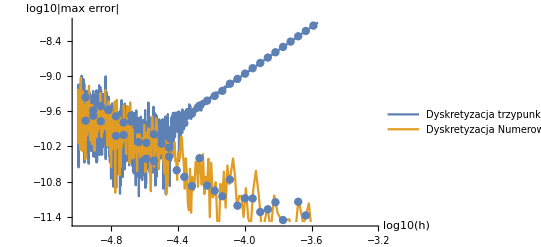

```mathematica
ListLinePlot[{errorsthreepoints, errorsnumerow},AxesLabel->{"log10(h)", "log10|max error|"}, PlotLegends->{"Dyskretyzacja trzypunktowa", "Dyskretyzacja Numerow'a"}, Mesh->100]
```

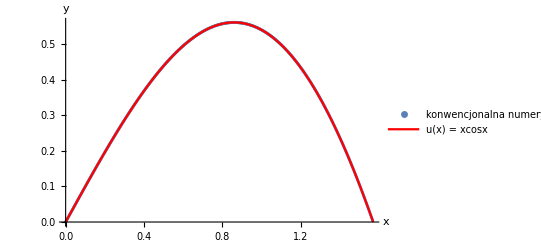

```mathematica
Show[ListPlot[res1,AxesLabel->{"x", "y"}, PlotLegends->{"konwencjonalna numerycznie (h = 10e-3)"}], Plot[x*Cos[x], {x, 0, π/2}, PlotLegends->{"u(x) = xcosx"}, PlotStyle->{Red}]]
```

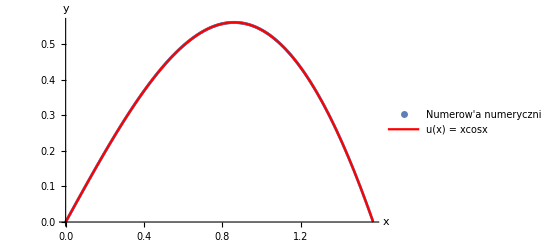

```mathematica
Show[ListPlot[res4,AxesLabel->{"x", "y"}, PlotLegends->{"Numerow'a numerycznie (h = 10e-3)"}], Plot[x*Cos[x], {x, 0, π/2}, PlotLegends->{"u(x) = xcosx"}, PlotStyle->{Red}]]
```